```mathematica
μ=0.62;
γ=5/3;
```

```mathematica
years=365.25*86400;
tEnd=10^3 years;
```

```mathematica
rper=0.7Rsun;
θper=45*Pi/180;
kRoss=21.1;
χ=(16*T[Rper,zper]^3*sigmaSB*(γ-1)*μ*mP)/(3*kRoss*ρ[Rper,zper]^2*kB);  (*this is what Goldreich and Schubert call χ*)
ξradiative = (γ-1)*χ     (*this is what Balbus and Schaan call ξrad*)

ν=23   (*from Menou&Balbus2004*)

η=596     (*from Menou&Balbus2004*)


Timing[Table[θper=θ;
Timing[ListofSolutions=Table[Timing[

M=Random[Integer,{-12.5,-3.5}];
kRexp=Random[Real,{M-1.5,M+1.5}];
kϕexp=Random[Real,{M-1.5,M+1.5}];
kzexp=Random[Real,{M-1.5,M+1.5}];
kR0=(-1)^Random[Integer,{0,1}](2Pi)/(10^kRexp Rsun);
kϕ0=(-1)^Random[Integer,{0,1}](2Pi)/(10^kϕexp Rsun);
kz0=(-1)^Random[Integer,{0,1}](2Pi)/(10^kzexp Rsun);
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vSqmod0=vR0^2+vz0^2;
SolveTheSystem;
vSqmod[t_]=δvRsol[t]^2+δvzsol[t]^2;
MaxVelocitySq=(Max[vSqmod[tEnd/10^6],vSqmod[tEnd/10^5],vSqmod[tEnd/10^4],vSqmod[tEnd/10^3],vSqmod[tEnd/10^2],vSqmod[tEnd/10^1],vSqmod[tEnd]])/vSqmod0;
{kR0,kϕ0,kz0,MaxVelocitySq}],{q,1,10^5}];

ListofSolutions={θ,Sort[ListofSolutions, #1[[2]][[4]] > #2[[2]][[4]] &]};
PutAppend[ListofSolutions,"C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\RandomWavevectorTests\\Model B\\Model B - 1 - No Magnetic Field\\Model B - Results.txt"];PutAppend[ListofSolutions[[2]][[1]][[2]],"C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\RandomWavevectorTests\\Model B\\Model B - 1 - No Magnetic Field\\Model B - Short Results.txt"]],{θ,5/180 Pi,85/180 Pi,10/180 Pi}]]
```

1.42619×10^7

23

596

NDSolve::mxst: Maximum number of 165770 steps reached at the point t == 7.78512×10^7.

InterpolatingFunction::dmval: Input value {3.15576×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.15576×10^9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
ListofSolutions
```

{(17 π)/36,{{0.03125,{1.58082×10^-6,0.0000242485,-3.43199×10^-8,0.987251}},{0.34375,{-9.26453×10^-7,-3.31661×10^-7,-1.23811×10^-7,0.972262}},{0.03125,{-0.000232852,-0.0000189697,0.0000582027,0.903727}},{0.,{-0.0000632878,-0.00129174,0.000574369,0.0545098}},{0.,{-0.000230315,-0.00237256,-0.00158907,6.91118×10^-6}},{0.03125,{0.175719,-0.148412,-0.0287332,5.04474×10^-20}},{0.01563,{-0.00405444,0.000952452,-0.00633601,1.65819×10^-21}},{0.03125,{0.00697484,0.170703,-0.213372,6.02731×10^-41}},{0.01563,{-7.72384,4.29284,0.0330695,7.85326×10^-45}},{0.01563,{-0.0264856,0.0016066,-0.154622,5.30498×10^-45}}}}

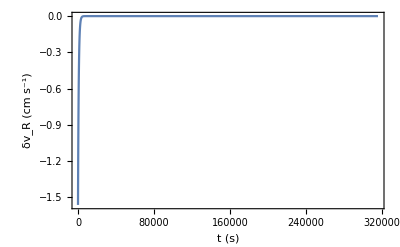

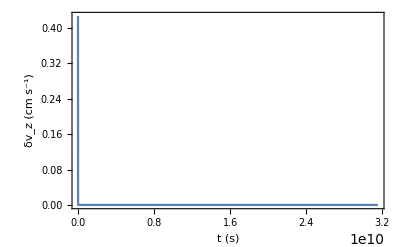

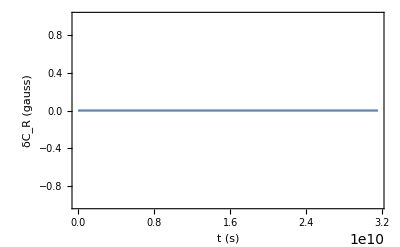

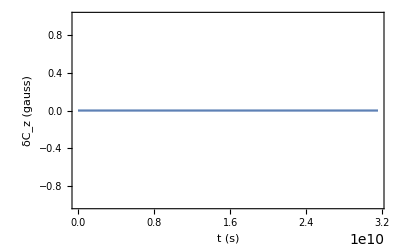

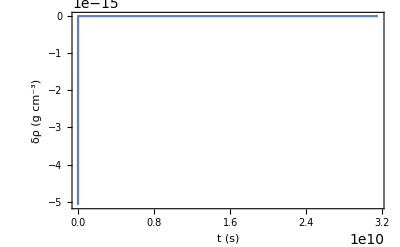

```mathematica
Plot[δvRsol[t],{t,0,tEnd/100000},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_R (cm s^-1)","Test 08 - δv_R(t)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δvzsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_z (cm s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δCRsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_R (gauss)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δCzsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_z (gauss)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δρsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δρ (g cm^-3)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
```